#### Notes

Maybe we can test random weights for some number of attempts then skip to next if none are found. This random search would reduce memory complexity of the algorithm. 
		First: Test random weights to reduce Graph List
	 	Second: Complete Test of all weights
	 	Third: ?
	
	Understanding the relationships between graphs would be nice. We could test the graphs in order of inclusion as a subgraph. So Construct a Poset of the graphs where the order is by inclusion as isomorphic subgraphs ( Not sure if this actually leads to a Poset structure but the idea is still there). Then perform tests according to the ordering.

#### Helper Functions

```mathematica
(*Helper Functions*)
PerfectDistanceQ[G_,w_]:=Union@*Flatten@*Round@GraphDistanceMatrix[Graph[G,EdgeWeight->w]] == Range[0,Binomial[VertexCount[G],2]];
WeightSets[Vn_,En_]:=Select[Subsets[Range[Binomial[Vn,2]],{En}],MemberQ[#,1]&&MemberQ[#,2]&] ;
ReduceWeightSets[W_,Vn_]:=Pick[W,Table[SubsetQ[(Total/@Subsets[W[[i]],Length[W[[i]]]]),Range[0,Binomial[Vn,2]]],{i,1,Length[W]}]]
ReduceWeightSetsDiam[W_,G_]:=Pick[W,Table[SubsetQ[(Total/@Subsets[W[[i]],GraphDiameter[G]]),Range[0,Binomial[VertexCount[G],2]]],{i,1,Length[W]}]]

TotalWeightings[G_] := EdgeCount[G]!Binomial[Binomial[VertexCount[G],2]-2,EdgeCount[G]-2];
StatusGraph[GraphList_,NPDG_,MPDG_]:=Module[{G,NPDGC,MPDGC},G =ResourceFunction["HasseDiagram"][IsomorphicSubgraphQ,CanonicalGraph/@GraphList];NPDGC=CanonicalGraph/@NPDG;MPDGC=CanonicalGraph/@MPDG; HighlightGraph[G,{Style[NPDGC,Red],Style[VertexOutComponent[G,MPDGC],Green],Style[MPDGC,Blue]},GraphLayout->"LayeredDigraphEmbedding",VertexLabels->MapIndexed[#->Placed[{VertexList[G][[#2[[1]]]]},{Tooltip}]&,VertexList[G]],EdgeStyle->Directive[Thin,Gray]]];
```

#### Code

```mathematica
MPDG = CanonicalGraph[#]&/@Import["/Users/alexanderhabib/MPDG7_Incomplete.mx"];
NPDG =CanonicalGraph[#]&/@Import["/Users/alexanderhabib/NPDG7_Incomplete.mx"];
(*Graphs = CanonicalGraph[#]&/@SortBy[Import["/Users/alexanderhabib/Desktop/Graphs/connected_graphs/n_7/graph7c.g6"],EdgeCount];*)
(*MinimalPerfectDistanceGraphs = MPDG;
NotPerfectDistanceGraphs = NPDG;

GraphList = Complement[Graphs,Union[NotPerfectDistanceGraphs,VertexOutComponent[ResourceFunction["HasseDiagram"][IsomorphicSubgraphQ,Graphs],MPDG]]];*)
```

Import::nffil: File /Users/alexanderhabib/MPDG7_Incomplete.mx not found during Import.

Import::nffil: File /Users/alexanderhabib/NPDG7_Incomplete.mx not found during Import.

```mathematica
Graphs = SortBy[Import["/Users/alexanderhabib/Desktop/PDG_UGR/Graphs/connected_graphs/n_6/graph6c.g6"], EdgeCount];
```

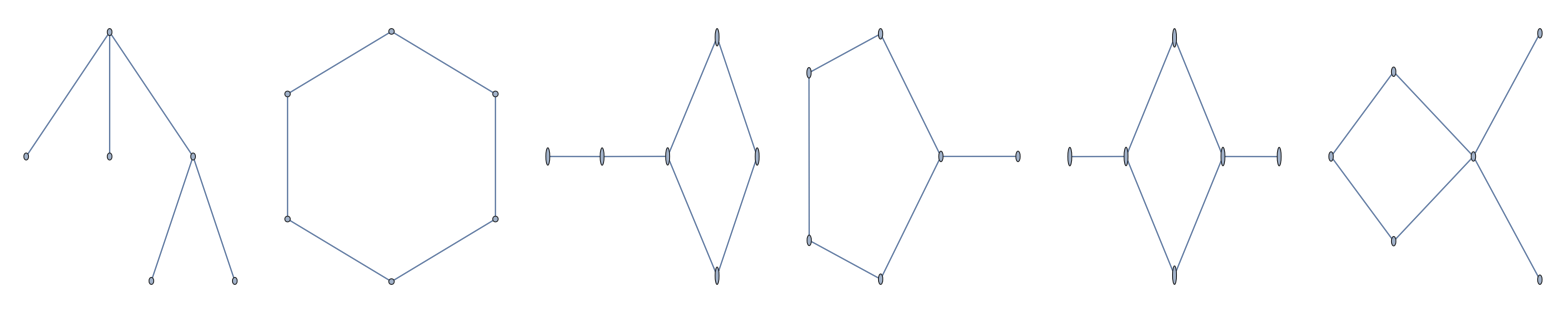
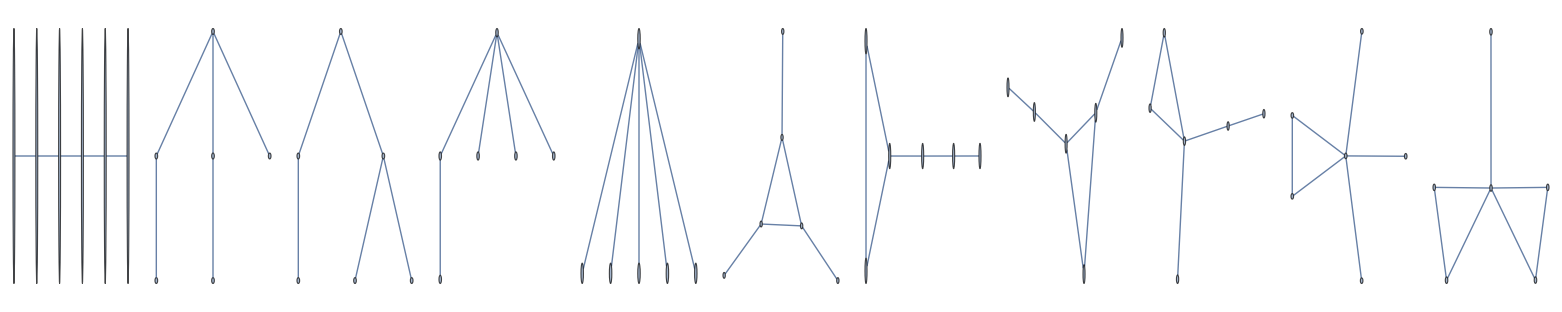
Time To Compute:	00:01:32TimeObject[{0,1,32.0806},Instant] and 80.626ms
Minimal Perfect Distance Graphs(6): 
-Graphics-
Not Perfect Distance Graphs(11): 
-Graphics-

```mathematica
GraphList = Graphs;

MinimalPerfectDistanceGraphs = {}; NotPerfectDistanceGraphs = {};
GraphWeightPairs = {};
SetSharedVariable[GraphWeightPairs]
TotalTime = AbsoluteTiming[
While[Length[GraphList]!=0,
GraphsGivenEdgeCount = First[GatherBy[GraphList,EdgeCount]];
VCount = VertexCount[GraphsGivenEdgeCount[[1]]];
ECount = EdgeCount[GraphsGivenEdgeCount[[1]]];

W = ReduceWeightSets[WeightSets[VCount ,ECount],VCount];

PDGs = {};
SetSharedVariable[PDGs];
DistributeDefinitions[PerfectDistanceQ,W];

ParallelDo[
weights = {};
Do[
WL = Permutations[Wi];
ResWi =Do[
If[PerfectDistanceQ[G,w],AppendTo[weights,w]]
,{w,WL}];
,{Wi,W}];

If[Length[weights]>0,AppendTo[PDGs,G];AppendTo[GraphWeightPairs,{G,weights}]]
,{G,GraphsGivenEdgeCount},Method->"FinestGrained",DistributedContexts->None];

GraphList = Complement[GraphList,GraphsGivenEdgeCount];

Do[GraphList = Select[GraphList,Not[IsomorphicSubgraphQ[PDG,#]]&],{PDG,PDGs}];

Do[AppendTo[MinimalPerfectDistanceGraphs,PDG],{PDG,PDGs}];
Do[AppendTo[NotPerfectDistanceGraphs,PDG],{PDG,Complement[GraphsGivenEdgeCount,PDGs]}];

]][[1]];


Print[
"Time To Compute:\t",TimeObject[{0,0,TotalTime}]," and ",1000FractionalPart[TotalTime],"ms\n",
"Minimal Perfect Distance Graphs(",Length[MinimalPerfectDistanceGraphs],"): \n",TableForm[MinimalPerfectDistanceGraphs,TableDirections->Row],"\n",
"Not Perfect Distance Graphs(",Length[NotPerfectDistanceGraphs],"): \n",
TableForm[NotPerfectDistanceGraphs,TableDirections->Row]
]

StatusGraph[Graphs,NotPerfectDistanceGraphs,MinimalPerfectDistanceGraphs];
```

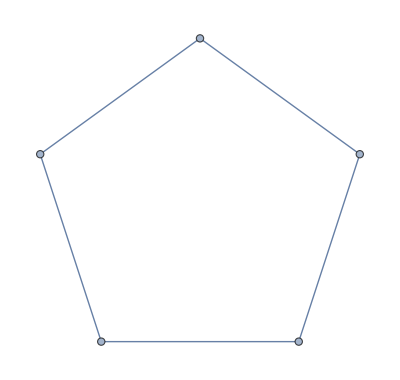
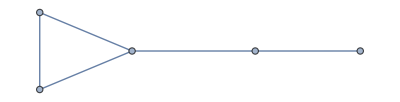
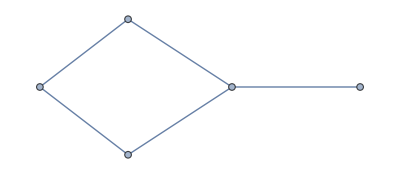
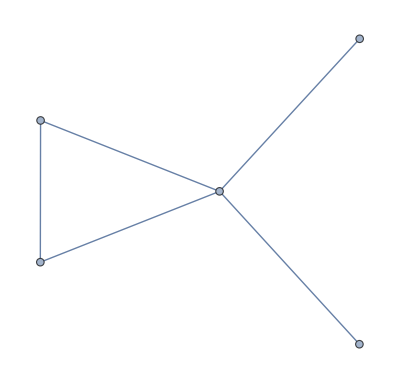
{{-Graphics-,{{1,3,10,2,5},{1,5,2,10,3},{2,5,1,3,10},{2,10,3,1,5},{3,1,5,2,10},{3,10,2,5,1},{5,1,3,10,2},{5,2,10,3,1},{10,2,5,1,3},{10,3,1,5,2},{1,2,6,10,4},{1,4,10,6,2},{2,1,4,10,6},{2,6,10,4,1},{4,1,2,6,10},{4,10,6,2,1},{6,2,1,4,10},{6,10,4,1,2},{10,4,1,2,6},{10,6,2,1,4}}},{-Graphics-,{{3,2,1,5,4},{3,4,1,5,2}}},{-Graphics-,{{2,3,9,7,1},{9,7,2,3,1},{4,5,8,2,1},{8,2,4,5,1},{4,1,6,8,2},{6,8,4,1,2},{7,2,8,4,1},{8,4,7,2,1},{7,1,9,4,2},{9,4,7,1,2}}},{-Graphics-,{{4,5,1,2,8},{4,5,2,1,8},{4,8,1,2,5},{4,8,2,1,5},{7,4,1,2,8},{7,4,2,1,8},{7,8,1,2,4},{7,8,2,1,4},{10,4,1,2,7},{10,4,2,1,7},{10,7,1,2,4},{10,7,2,1,4}}}}

```mathematica
GraphWeightPairs
```

```mathematica
(*Non Isomorphic Weightings*)
C6 = GraphWeightPairs[[4]];
G = C6[[1]];
PWL = C6[[2]];

EdgeAutG= GraphAutomorphismGroup[LineGraph[G]];

DeleteDuplicates[PWL,If[Sort[#1]==Sort[#2],GroupElementQ[EdgeAutG,FindPermutation[#1,#2]],False]&]
```

{{3,2,4,14,1,7},{8,1,10,3,2,4},{8,1,12,3,4,2},{5,2,6,3,1,14},{7,2,14,5,1,3},{3,1,11,7,8,2},{2,9,13,7,1,3},{5,4,6,13,1,2},{5,4,7,13,2,1},{4,8,5,9,1,2},{8,4,9,5,1,2},{1,8,5,10,4,2},{2,1,10,5,8,4},{8,4,10,5,2,1},{1,2,9,6,8,4},{4,8,6,9,2,1},{2,6,10,11,4,1},{7,11,9,4,2,1}}

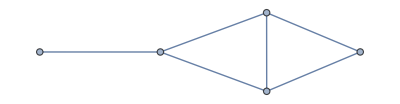
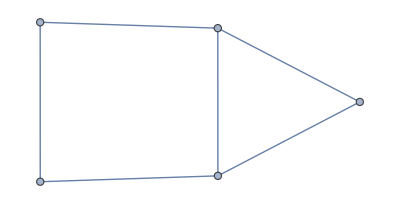
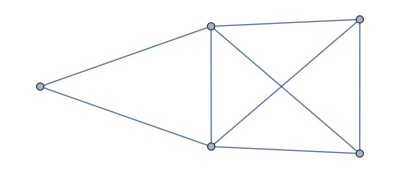
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

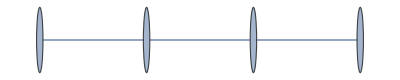
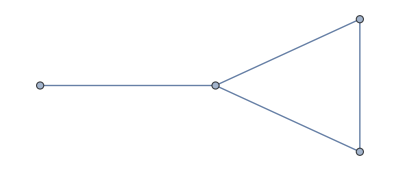
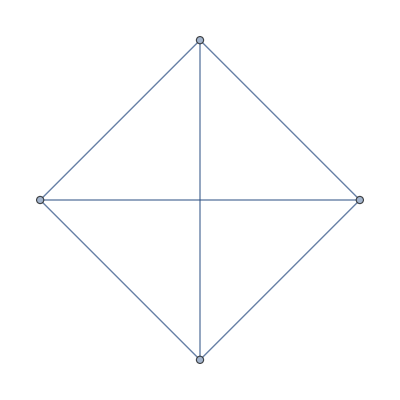
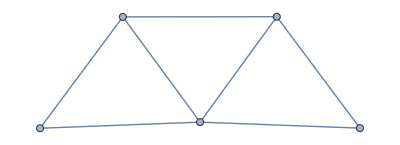

```mathematica
LineGraph/@MinimalPerfectDistanceGraphs
LineGraph/@NotPerfectDistanceGraphs
```

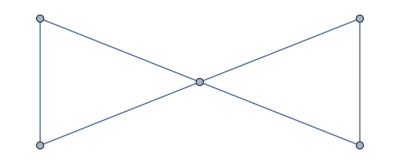
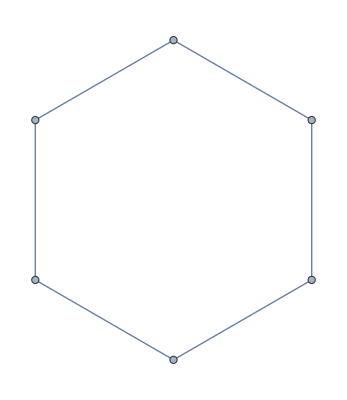
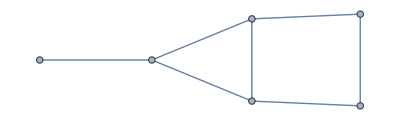
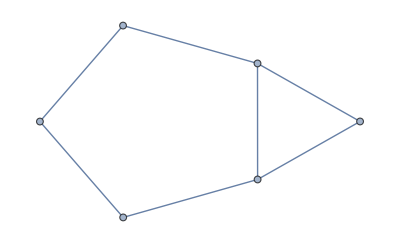
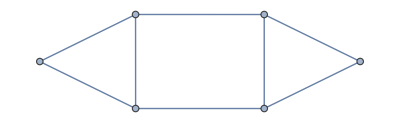
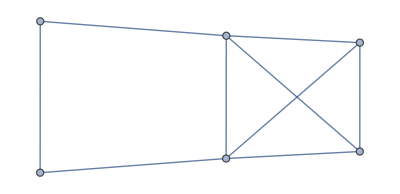

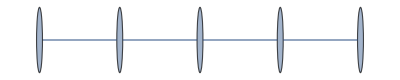
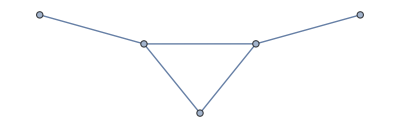

```mathematica
LineGraph/@MinimalPerfectDistanceGraphs
LineGraph/@NotPerfectDistanceGraphs
```